```mathematica
$Assumptions={ M>0,R>2M}
```

{True,True}

```mathematica
Clear[R,M,l]
```

```mathematica
A0[r_] := 1/(4 R^3)( Sqrt[R^3-2 M r^2] - 3 R Sqrt[ R - 2M] )^2;
B0[r_] := (1-2M*r^2/R^3)
ρ0= (3 M)/(4π R^3);
p0[r_] = ρ0*(Sqrt[ 3 - 8π R^2 ρ0]- Sqrt[ 3 - 8π r^2 ρ0])/(Sqrt[ 3 - 8π r^2 ρ0]- 3 Sqrt[ 3 - 8π R^2 ρ0]);
f0[r_] = 1-2M/r ;
dd[x_] := If[x==0,1,0];
Vin0[r_,s_] := A0[r]*((l(l+1))/r^2+(1-s^2)/(2*r)B0[r](A0'[r]/A0[r]+B0'[r]/B0[r]) + 8 π * (p0[r]-ρ0)*dd[s-2]);
Vout0[r_,s_] := f0[r]*((l(l+1))/r^2+(1-s^2)/r f0'[r]);
V0[r_,s_] := Piecewise[ {{Vin0[r,s], r≤ R}, {Vout0[r,s], r>R}}];
ΔVs2= Vin0[R,2]-Vout0[R,2]//FullSimplify
ΔVs0= Vin0[R,0]-Vout0[R,0]//FullSimplify
```

(3 (2 M-R) (3 M R √(-2 M+R)-5 M √(R^2 (-2 M+R))+l (1+l) R (R √(-2 M+R)-√(R^2 (-2 M+R)))))/(2 R^4 √(R^2 (-2 M+R)))

(3 (2 M-R) (-3 M R √(-2 M+R)+5 M √(R^2 (-2 M+R))+l (1+l) R (R √(-2 M+R)-√(R^2 (-2 M+R)))))/(2 R^4 √(R^2 (-2 M+R)))

```mathematica
(*Interesting that ΔV is the same magnitude for both spins, but different signs*)
```

```mathematica
M=1; R=226/100; l=2;
```

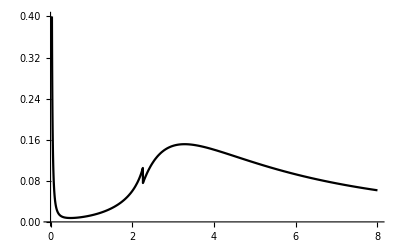

```mathematica
Plot[ V0[r,2], {r,0,8}, Exclusions->None, PlotRange-> {Automatic,{0,0.4}}, PlotStyle->Black]
```

```mathematica
rpeak0= r/.NSolve[D[Vout0[r,0],r]==0&&r>2,r]//First
rpeak2= r/.NSolve[D[Vout0[r,2],r]==0&&r>2,r]//First
```

2.95171

3.28078

```mathematica
Clear[M,R,l,rstin0,rstout0,V0ints0in,V0ints0out,V0ints0,V0ints2in ,V0ints2out ,V0ints2]
```

```mathematica
rstin0[r_]= Integrate[1/Sqrt[A0[r]*B0[r]],r];
```

```mathematica
M=1; R=226/100; l=2; 
(*rstin0[r_]:= NIntegrate[1/Sqrt[A0[rr]*B0[rr]],{rr,0,r}]*)
rstout0[r_] = r+2*M*Log[r/(2M)-1]- R-2*M*Log[R/(2M)-1]+rstin0[R];
V0ints0in = Interpolation[ Table[ N[{Re[rstin0[r]],V0[r,0]}],{r,R/100,R,R/100}],InterpolationOrder->6];
V0ints0out = Interpolation[ Table[ N[{Re[rstout0[r]],V0[r,0]}],{r,R+R/10000,50R+R/10000,R/100}] ,InterpolationOrder->6];
V0ints0[x_] := Piecewise[ {{ V0ints0in[x],x≤  Re[rstin0[R]]} ,{  V0ints0out[x],x> Re[rstin0[R]] }}    ]
```

```mathematica
V0ints2in = Interpolation[ Table[ N[{Re[rstin0[r]],V0[r,2]}],{r,R/100,R,R/100}], InterpolationOrder->6];
V0ints2out = Interpolation[ Table[ N[{Re[rstout0[r]],V0[r,2]}],{r,R+R/10000,50R+R/10000,R/100}],InterpolationOrder->6 ];
V0ints2[x_] := Piecewise[ {{ V0ints2in[x],x≤ Re[rstin0[R]]} ,{  V0ints2out[x],x> Re[rstin0[R]] }}    ]
```

```mathematica
Rs = Re[N[rstin0[R]]]
Rp0 = Re[N[rstout0[rpeak0]]]
Rp2 = Re[N[rstout0[rpeak2]]]
```

73.4889

76.7758

77.6987

```mathematica
{xmin,xmax}=N[{Re[rstin0[R/100]],Re[rstout0[R*(50)]]}]
```

{2.57408,196.342}

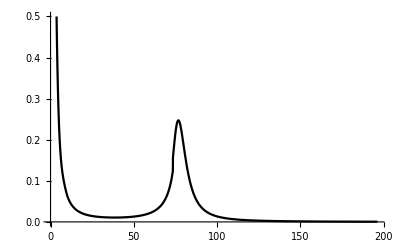

```mathematica
plt1 = Plot[ V0ints0[x], {x,xmin,xmax}, Exclusions->None, PlotRange-> {{0,xmax},{0,.5}}, PlotStyle->Black]
```

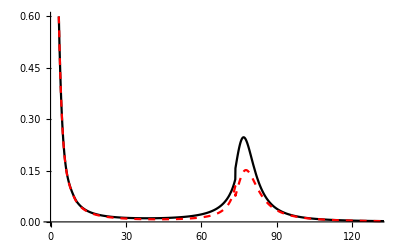

```mathematica
plt1 = Plot[ {V0ints0[x],V0ints2[x]} ,{x,xmin,xmax}, Exclusions->None, PlotRange-> {{0,130},{0,.6}}, PlotStyle->{Black,{Red,Dashed}}]
```

```mathematica
line = Line[ {{Rs,0},{Rs,V0ints0[Rs]}}];
line0 = Line[ {{Rp0,0.3},{Rp0,V0ints0[Rp0]}}];
line2 = Line[ {{Rp2,0.3},{Rp2,V0ints2[Rp2]}}];
```

```mathematica
sz=16;
ticks = { { None,None}, {{ {Rs,Style["R_*",Black,sz]},{0,Style["0",Black,sz]} (*,{Rp2,Style["r_(*2)",Black,sz]}*)}, None}};
```

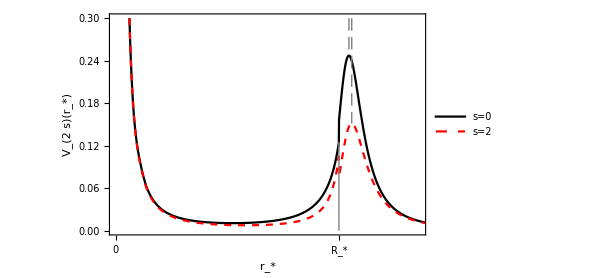

```mathematica
pltexp=Plot[{V0ints0[x],V0ints2[x]},{x,xmin,xmax}, Exclusions->None, PlotRange-> {{0,100},{0,.3}},PlotStyle-> {Black, {Red,Dashed}},(* PlotPoints -> 30,*) PlotLegends->Placed[ LineLegend[{Style["s=0",20,Black,FontFamily->"Bookman Old Style"], Style["s=2",20,Black,FontFamily->"Bookman Old Style"]}], {.3,.8}] , ImageSize->450, Frame->True, FrameTicks->ticks,FrameStyle-> {{Directive[Black],Directive[Black]},{Directive[Black],Directive[Black]}}, FrameLabel->{Style["r_*",20,Black,FontFamily->"Bookman Old Style"], Style["V_(2  s)(r_*) ",20,Black,FontFamily->"Bookman Old Style"]} , FrameTicks->None, Epilog->{{Directive[Gray(*,Dashing[{0.02,0.02}]*),Thin ], line},{Directive[Gray,Dashing[{0.02,0.01}],Thin ],line0,line2}}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["potentials_s02_CD_R2p26L2.pdf",pltexp]
```

C:\Users\tstra\Dropbox\QNM_RP_star\code\Tom

potentials_s02_CD_R2p26L2.pdf